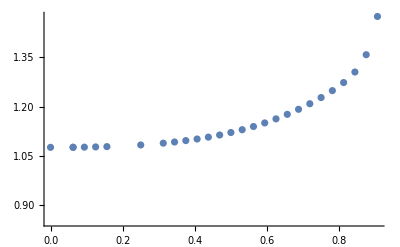

```mathematica
a4={{0,6.313705},{0.062500,6.309771},{0.062500,6.309771},{0.093750,6.368520},{0.125000,6.424554},{0.156250,6.489058},{0.187500,6.563377},{0.218750,6.647642},{0.250000,6.741820},{0.281250,6.845929},{0.312500,6.960103},{0.343750,7.084594},{0.375000,7.219776},{0.406250,7.366142},{0.437500,7.524296},{0.468750,7.694947},{0.500000,7.878910},{0.531250,8.077097},{0.562500,8.290516},{0.593750,8.520270},{0.625000,8.767552},{0.656250,9.033655},{0.687500,9.319972},{0.718750,9.628014},{0.750000,9.959433},{0.781250,10.316059},{0.812500,10.699957},{0.843750,11.113503},{0.875000,11.559492},{0.906250,12.041271}};
aa4={{0,5.238260},{0.062500,5.234179},{0.062500,5.234179},{0.093750,5.292505},{0.125000,5.347859},{0.156250,5.411392},{0.187500,29.776953},{0.218750,27.780364},{0.250000,5.659143},{0.281250,27.771327},{0.312500,5.871897},{0.343750,5.992808},{0.375000,6.123783},{0.406250,6.265240},{0.437500,6.417702},{0.468750,6.581795},{0.500000,6.758237},{0.531250,6.947843},{0.562500,7.151518},{0.593750,7.370261},{0.625000,7.605168},{0.656250,7.857437},{0.687500,8.128374},{0.718750,8.419387},{0.750000,8.731954},{0.781250,9.067461},{0.812500,9.426686},{0.843750,9.808032},{0.875000,10.201205},{0.906250,10.566154}};
A4=a4-aa4*Table[{0,1},{i,0,29}];
ListPlot[{A4}]
```

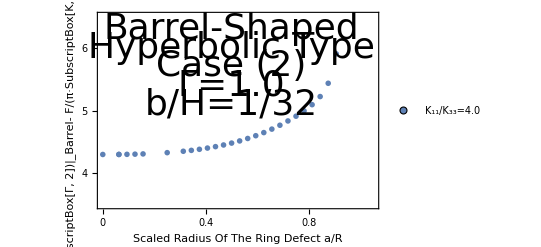

```mathematica
AA4=A4*Table[{1,4},{i,0,29}];
ListPlot[{AA4},PlotStyle->PointSize[0.01], Frame->{True, True, True, True}, FrameTicks->{{{4,5,6},None},{{0,0.2, 0.4, 0.6, 0.8,1},None}}, PlotRange->{{0,1.05},{3.5,6.5}},FrameLabel->{{"F/(π·SubscriptBox[K, 33] H SuperscriptBox[Γ, 2])|_Barrel- F/(π·SubscriptBox[K, 33] H SuperscriptBox[Γ, 2])|_Cylinder", None},{"Scaled Radius Of The Ring Defect a/R", None}},FrameTicksStyle->Directive[Black,36],FrameStyle->Thickness[0.005],LabelStyle->Directive[Black,36],PlotLegends->Placed[PointLegend[{"K_11/K_33=4.0"},LegendMarkers->{{Graphics[Disk[]],12}}],{Right,Bottom}],Epilog->{Text[Style["Barrel-Shaped",Directive[Black,36]],{0.5,6.3}],Text[Style["Hyperbolic Type",Directive[Black,36]],{0.5,6.0}],Text[Style["Case (2)",Directive[Black,36]],{0.5,5.7}],Text[Style["Γ=1.0",Directive[Black,36]],{0.5,5.4}],Text[Style["b/H=1/32",Directive[Black,36]],{0.5,5.1}]}]
```